Sound

In the Wolfram Language, sound works a lot like graphics, except that instead of having things like circles, one has sound notes. Press the play  button to actually play sounds. If you don’t say otherwise, the Wolfram Language will make the notes sound as if they were played on a piano.

Generate a middle C note:

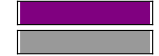

```mathematica
Sound[SoundNote["C"]]
```

You can specify a sequence of notes by giving them in a list.

Play three notes in sequence:

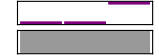

```mathematica
Sound[{SoundNote["C"],SoundNote["C"],SoundNote["G"]}]
```

Instead of giving names of notes, you can give a number to specify their pitch. Middle C is 0. Each semitone above middle C goes up by 1. Middle G is 7 semitones above middle C, so it’s specified by the number 7. (An octave is 12 semitones.)

Specify the notes by numbers:

```mathematica
Sound[{SoundNote[0],SoundNote[0],SoundNote[7]}]
```

-Graphics-

Use Table to generate a sequence of 5 notes:

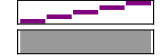

```mathematica
Sound[Table[SoundNote[n],{n,5}]]
```

If you don’t say otherwise, each note lasts 1 second. Use SoundNote[pitch,length]  to get a different length.

Play each note for 0.1 seconds:

```mathematica
Sound[Table[SoundNote[n,0.1],{n,5}]]
```

-Graphics-

In addition to piano, SoundNote can handle a long list of possible instruments. The name of each instrument is a string.

Play notes on a simulated violin:

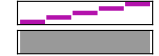

```mathematica
Sound[Table[SoundNote[n,0.1,"Violin"],{n,5}]]
```

It’s easy to make “random music”—different every time you generate it.

Play a sequence of 20 notes with random pitches:

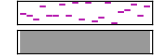

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.1,"Violin"],20]]
```

Vocabulary

Sound[{...}] |   | create a sound from notes 
SoundNote["C"] |   | a named note 
SoundNote[5] |   | a note with a numbered pitch 
SoundNote[5,0.1] |   | a note played for a specified time 
SoundNote[5,0.1,"Guitar"] |   | a note played on a certain instrument

"10 Exercises Available"
"with 4 extras" | "Get Started »"

Generate the sequence of notes with pitches 0, 4 and 7. »

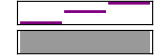
| Expected output: |  
  | -Graphics- |

Generate 2 seconds of playing middle A on a cello. »

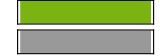
| Expected output: |  
  | -Graphics- |

Generate a “riff” of notes from pitch 0 to pitch 48 in steps of 1, with each note lasting 0.05 seconds. »

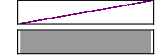
| Expected output: |  
  | -Graphics- |

Generate a sequence of notes going from pitch 12 down to 0 in steps of 1. »

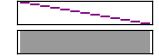
| Expected output: |  
  | -Graphics- |

Generate a sequence of 5 notes starting with middle C, then successively going up by an octave at a time. »

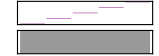
| Expected output: |  
  | -Graphics- |

Generate a sequence of 10 notes on a trumpet with random pitches from 0 to 12 and duration 0.2 seconds. »

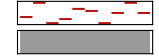
| Sample expected output: |  
  | -Graphics- |

Generate a sequence of 10 notes with random pitches up to 12 and random durations up to 10 tenths of a second. »

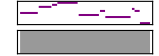
| Sample expected output: |  
  | -Graphics- |

Generate 0.1-second notes with pitches given by the digits of 2^31. »

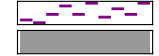
| Expected output: |  
  | -Graphics- |

Create a sound from the letters in CABBAGE, each playing for 0.3 seconds sounding like a guitar. »

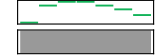
| Expected output: |  
  | -Graphics- |

Generate 0.1-second notes with pitches given by the letter numbers of the characters in “wolfram”. »

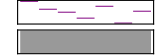
| Expected output: |  
  | -Graphics- |

Generate a sequence of three notes of 1 second of playing middle D on the cello, piano and guitar.  »

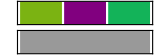
| Expected output: |  
  | -Graphics- |

Generate a sequence of notes from pitch 0 to pitch 12, going up in steps of 3.  »

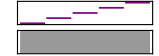
| Expected output: |  
  | -Graphics- |

Generate a sequence of 5 notes starting with middle C, then successively going up by a perfect fifth (7 semitones) at a time.  »

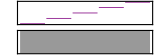
| Expected output: |  
  | -Graphics- |

Generate 0.02-second notes with pitches given by the lengths of the names of integers from 1 to 200. »

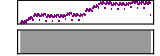
| Expected output: |  
  | -Graphics- |

Q&A

What are the pictures that the Wolfram Language displays for Sound?

They’re like musical scores, where the pitch of each note is represented by its height. The duration of the note is represented by its horizontal length in piano roll style, rather than with ♩, ♪, etc.

How do I know which instruments are available?

Look at the list under “Details and Options” in the SoundNote reference page, or just start typing and see the completions you’re offered. You can also use instrument numbers, from 1 to 128. All the standard MIDI instruments are there, including percussion.

How do I play notes below middle C?

Just use negative numbers, like SoundNote[-10].

What are sharp and flat notes called?

E# (E sharp), Ab (A flat), etc. They also have numbers (e.g. E# is 5). The # and b can be typed as ordinary keyboard characters (though special ♯ and ♭ characters are available too).

How do I make a chord?

Put note names in a list, as in SoundNote[{"C","G"}].

How do I make a rest?

For a 0.2-second rest, use SoundNote[None,0.2].

How do I get a sound to play immediately, without having to press the play button?

Use EmitSound, as in EmitSound[Sound[SoundNote["C"]]], etc.

Why do I need quotes in the name of a note like “C”?

Because the name is a Wolfram Language string. If you typed just C, it would be interpreted as a function named C, which isn’t what you want.

Can I record audio and manipulate it?

Yes. Use AudioCapture, then use functions like AudioPlot, Spectrogram, AudioPitchShift, etc., as in Section 46.

Tech Notes

SoundNote corresponds to MIDI sound. The Wolfram Language also supports “sampled sound”, for example using functions like ListPlay, as well as an Audio construct that represents all aspects of an audio signal (see Section 46).

To get spoken output, use Speak. To make a beep, use Beep.

More to Explore

Guide to Sound Generation in the Wolfram Language »